# Chuliang Song, György Barabas, Serguei Saavedra. “On the consequences of the interdependence of stabilizing and equalizing mechanisms”, The American Naturalist, In Press.

## This Mathematica file reproduces the five figures in the main text.

```mathematica
AddLabel[x_,label_]:=Labeled[x,Style[label,FontSize->18],{{Left,Top}}];
```

## Figure 1

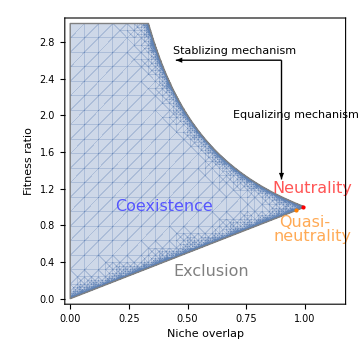

~/Dropbox (MIT)/应用/Overleaf/Inconsistency in MCT/Figure1.pdf

```mathematica
Show[
RegionPlot[x y<=1&&y>=x,{x,0,1.15},{y,0,3},MaxRecursion->10,
FrameLabel->{Style["Niche overlap",18],Style["Fitness ratio",18]},
FrameTicks->{Automatic,Automatic},
BoundaryStyle->{Gray,Thin},
ImageSize->Medium
],
Graphics[{
Text[Style["Coexistence",16,Lighter@Blue],{0.4,1}],
Text[Style["Stablizing mechanism",Medium],{0.7,2.7}],
Arrow[{{.9,2.6},{0.45,2.6}}],
Rotate[Text[Style["Equalizing mechanism", Medium],{.96,2}],90 Degree],
Arrow[{{.9,2.6},{.9,1.3}}],
{PointSize[Large],Red,Point[{.99,1}]},
Text[Style["Neutrality",16,Lighter@Red],{1.03,1.2}],
Text[Style["Exclusion",16,Gray],{0.6,.3}],
{PointSize[Large],Orange,Point[{.96,.97}]},
Text[Style["Quasi-",16,Lighter@Orange],{1,.83}],
Text[Style["neutrality",16,Lighter@Orange],{1.03,.68}]
}]
]
Export["~/Dropbox (MIT)/应用/Overleaf/Inconsistency in MCT/Figure1.pdf",%]
```

## Figure 2

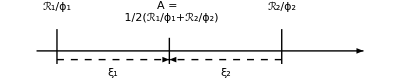

~/Dropbox (MIT)/应用/Overleaf/Inconsistency in MCT/Figure2.pdf

```mathematica
a=0.05;b=0.6;
Show[
Graphics[{
{Arrowheads[0.05],Thick,Arrow[{{0,0},{0.8,0}}]},
{Line[{{a,0},{a,0.05}}]},
{Text["ℛ_1/ϕ_1",{a,0.1}]},
{Line[{{b,0},{b,0.05}}]},

{Text["ℛ_2/ϕ_2",{b,0.1}]},
{Line[{{a/2+b/2,0},{a/2+b/2,0.03}}]},
{Text["A = \n 1/2(ℛ_1/ϕ_1+ℛ_2/ϕ_2)",{a/2+b/2,0.09}]},
{Line[{{a,0},{a,-0.03}}]},
{Line[{{b,0},{b,-0.03}}]},
{Line[{{a/2+b/2,0},{a/2+b/2,-0.03}}]},
{Dashed,Arrowheads[0.02],Arrow[{{a,-0.02},{a/2+b/2,-0.02}}]},
{Dashed,Arrowheads[0.02],Arrow[{{b,-0.02},{a/2+b/2,-0.02}}]},
{Text[Style["ξ_1",Medium],{Mean[{a,Mean[{a,b}]}],-0.05}]},
{Text[Style["ξ_2",Medium],{Mean[{b,Mean[{a,b}]}],-0.05}]}
}]
]
Export["~/Dropbox (MIT)/应用/Overleaf/Inconsistency in MCT/Figure2.pdf",%]
```

## Figure 3

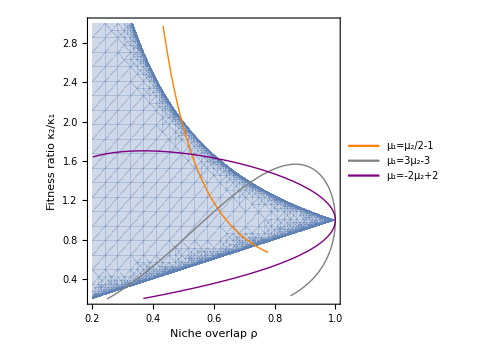

~/Dropbox (MIT)/应用/Overleaf/Inconsistency in MCT/Figure3.pdf

```mathematica
σ=1;
ω=.5;
Show[
RegionPlot[x y<=1&&y>=x,{x,0.2,1},{y,0.2,3},MaxRecursion->10,FrameLabel->{Style["Niche overlap ρ",20],Style["Fitness ratio κ_2/κ_1",20]},FrameTicks->{Automatic,Automatic},
ImageSize->Medium,
AspectRatio->1,
BoundaryStyle->None,
PlotLegends->Placed[Style[LineLegend[{Orange,Gray,Purple},
{"μ_1=μ_2/2-1","μ_1=3μ_2-3","μ_1=-2μ_2+2"}],12],{Right,Top}]
],
ParametricPlot[{Exp[-(x-y)^2/(4σ^2)],Exp[-(x^2-y^2)/(2 σ^2+2ω^2)]}
/.{x->y/2-1},
{y,0,1.66},AspectRatio->Full,PlotStyle->{Orange,Thick}],
ParametricPlot[{Exp[-(x-y)^2/(4σ^2)],Exp[-(x^2-y^2)/(2σ^2+2ω^2)]}
/.{x->3y-3},
{y,.32,1.9},AspectRatio->Full,PlotStyle->{Gray,Thick}],
ParametricPlot[{Exp[-(x-y)^2/(4σ^2)],Exp[-(x^2-y^2)/(2σ^2+2ω^2)]}
/.{x->-2y+2}
 ,{y,0,1.51},AspectRatio->Full,PlotStyle->{Purple,Thick}]
]
Export["~/Dropbox (MIT)/应用/Overleaf/Inconsistency in MCT/Figure3.pdf",%]
```

## Figure 4

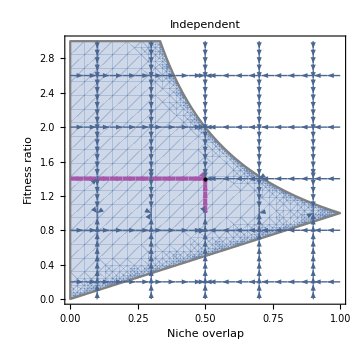
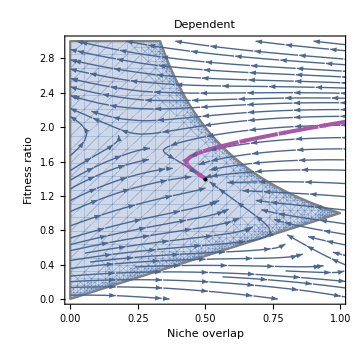
-Graphics-A | -Graphics-B

~/Dropbox (MIT)/应用/Overleaf/Inconsistency in MCT/Figure4.pdf

```mathematica
p = {.5,1.4};
Show[
RegionPlot[x y<=1&&y>=x,{x,0,1},{y,0,3},MaxRecursion->5,
FrameLabel->{Style["Niche overlap",18],Style["Fitness ratio",18]},
FrameTicks->{Automatic,Automatic},
(*FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],*)
BoundaryStyle->{Gray,Thin},
ImageSize->Medium,
PlotLabel->Style["Independent",24]
],
StreamPlot[{1,0},{x,0,.5},{y,0,3},StreamPoints->{{{.3,.2},{.3,.8},{.3,2},{.3,2.6}}}],
StreamPlot[{1,0},{x,0,.5},{y,0,3},StreamPoints->{p},StreamStyle->{Lighter@Purple,Thickness[.008]}],
StreamPlot[{-1,0},{x,.5,1},{y,0,3},StreamPoints->{{p,{.5,.2},{.5,.8},{.5,2},{.5,2.6}}}],
StreamPlot[{0,-1},{x,0,1},{y,1,1.4},StreamPoints->{{{.1,1},{.3,1},{.7,1},{.9,1}}}],
StreamPlot[{0,1},{x,0,1},{y,1,1.4},StreamPoints->{p},StreamStyle->{Lighter@Purple,Thickness[.008]}],
StreamPlot[{0,-1},{x,0,1},{y,1.4,3},StreamPoints->{{p,{.1,1.4},{.3,1.4},{.7,1.4},{.9,1.4}}}],
StreamPlot[{0,1},{x,0,1},{y,0,1},StreamPoints->{{{.1,1},{.3,1},{.5,1},,{.7,1},{.9,1}}}],
Graphics[{
{PointSize[Large],Point[p]}
}]
];
Show[
RegionPlot[x y<=1&&y>=x,{x,0,1},{y,0,3},MaxRecursion->5,
FrameLabel->{Style["Niche overlap",18],Style["Fitness ratio",18]},
FrameTicks->{Automatic,Automatic},
BoundaryStyle->{Gray,Thin},
ImageSize->Medium,
PlotLabel->Style["Dependent",24]
],
StreamPlot[{2.7999999999999985-2.799999999999999 x-y-3*(x-.5)^2-(y-1.4)^3,1.8666666666666667-0.9333333333333333 x-y+3*(x-.5)^2+(y-1.4)^3},{x,0,2},{y,0,3}],
StreamPlot[{2.7999999999999985-2.799999999999999 x-y,1.8666666666666667-0.9333333333333333 x-y},{x,0,2},{y,0,3},StreamPoints->{p},StreamStyle->{Lighter@Purple,Thickness[.008]}],
Graphics[{
{PointSize[Large],Point[p]}
}]
];
Grid[{{AddLabel[%%,"A"],AddLabel[%,"B"]}},Spacings->{2,2},Frame->None]
Export["~/Dropbox (MIT)/应用/Overleaf/Inconsistency in MCT/Figure4.pdf",%]
```

## Figure 5

### Panel A

```mathematica
p1 = {1,1};
p2={1,.9};
p3 = {.9,.9};
Figure5A = Show[
RegionPlot[x y<=1&&y≥x,{x,0.1,1.1},{y,0.3,1.3},MaxRecursion->8,FrameLabel->{Style["Niche overlap",18],Style["Fitness ratio",18]},
FrameTicks->{Automatic,Automatic},
(*FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],*)
BoundaryStyle->{Gray,Thin},
ImageSize->Medium,
PlotLegends->Placed[Style[LineLegend[{Black,Dashed},
{"Independent","Dependent"}],12],{Right,Bottom}]
],
Graphics[{
{PointSize[.02],Lighter@Red,Point[p1]},
{PointSize[.02],Point[p2]},
{PointSize[.02],Point[p3]},
{PointSize[.02],Point[{.4,.4}]},
{Thin,Arrow[BezierCurve[{p2,{0.9,0.9}}]]},
{Dashed,Thick,Arrow[BezierCurve[{p2,{.8,.4},{.4,.4}}]]},
Text[Style["α",14,Bold,Gray],{1.03,.9}],
Text[Style["β",14,Bold,Gray],{.86,.9}],
Text[Style["γ",14,Bold,Gray],{.37,.4}]
}]
];
```

### Panel B

```mathematica
a=0.45;
ratio=0.8;
Figure5B=Show[
RegionPlot[Abs[y-x]>ratio Abs[x]&&y>x,{x,0,1},{y,0,1},
ImageSize->Medium,
BoundaryStyle->None,
AspectRatio->1,
FrameLabel->{Style["Species 1 niche center μ_1",18],Style["Species 2 niche center μ_2",18]}
],
RegionPlot[Abs[y-x]>ratio Abs[x]&&y<x,{x,0,1},{y,0,1},
ImageSize->Medium,
BoundaryStyle->None,
AspectRatio->1,
FrameLabel->{Style["Species 1 niche center μ_1",20],Style["Species 2 niche center μ_2",20]},
FrameTicks->None
],
Plot[x,{x,0,1},
PlotStyle->{RGBColor[0.8,0.15,0.15],Thick}],
Graphics[{
{Arrowheads[{-.05,.05}],Arrow[{{a,a},{a,a*(1+ratio)}}]},
Text[Style["Abs[Δμ]",16],{a+0.07,Mean[{a,a*(1+ratio)}]}],
Text[Style["Coexistence",16,Lighter@Blue],{0.18,0.7}],
Text[Style["Coexistence",16,Lighter@Blue],{0.8,0.07}],
Text[Style["Neutrality",16,Lighter@Red],{0.86,0.7}],
Text[Style["Exclusion",16,Gray],{0.77,.4}]
}]
];
```

### Combined Figure 5

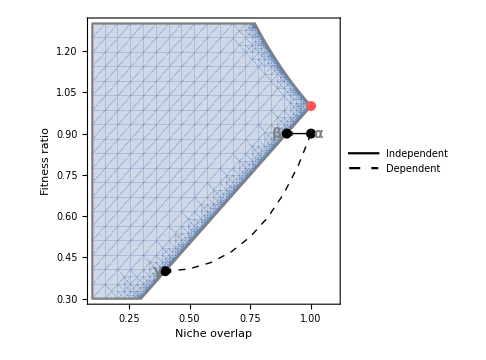
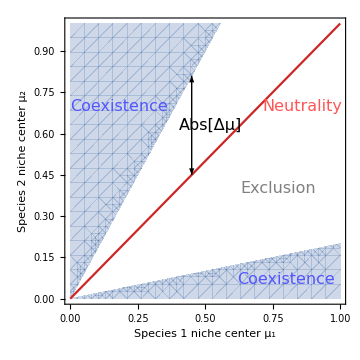
-Graphics-A | -Graphics-B

~/Dropbox (MIT)/应用/Overleaf/Inconsistency in MCT/Figure5.pdf

```mathematica
Grid[{{AddLabel[Figure5A,"A"],AddLabel[Figure5B,"B"]}},Spacings->{2,2},Frame->None]
Export["~/Dropbox (MIT)/应用/Overleaf/Inconsistency in MCT/Figure5.pdf",%]
```